```mathematica
nex[L_]:=Module[{},
i=2;
While[i<=Length[L]&&(t=Rest[Flatten[Take[L,-i]]];First[t]==Max[t]),i++];
If[i>Length[L],Return[0]];s=Min[Select[t,#>First[t]&]];
LL=ReplacePart[L,s,{-i,2}];
Drop[LL,1-i]~Join~Partition[Complement[t,{s}],2]]
```

```mathematica
d[{{x1_,y1_},{x2_,y2_}}]:=(x1-x2)^2+(y1-y2)^2
```

```mathematica
house[{x_,y_}]:={AbsoluteThickness[1],Hue[.35],Polygon[{{x+.2,y+.2},{x+.8,y+.2},{x+.8,y+.5},{x+.5,y+.8},{x+.2,y+.5}}],GrayLevel[0],Line[{{x+.2,y+.2},{x+.8,y+.2},{x+.8,y+.5},{x+.5,y+.8},{x+.2,y+.5},{x+.2,y+.2}}]}
```

```mathematica
house[{x_,y_}]:={AbsoluteThickness[1],Hue[.35],Disk[{x+.5,y+.5},.3],GrayLevel[0],Circle[{x+.5,y+.5},.3]}
```

```mathematica
pic:={Print[Style[Show[Graphics[{Line[{{1,1},{1,size+1},{size+1,size+1},{size+1,1},{1,1}}],house/@pts}],AspectRatio->Automatic,ImageSize->30 size,PlotRange->{{1-.01,size+1.01},{1-.01,size+1.01}}],Antialiasing->False]];Print[Style[Show[Graphics[{Line[{{1,1},{1,size+1},{size+1,size+1},{size+1,1},{1,1}}],AbsoluteThickness[3],Hue[0.8],(Line[{pts⟦#1⟦1⟧⟧+{1/2,1/2},pts⟦#1⟦2⟧⟧+{1/2,1/2}}]&)/@ans1,Hue[0.1],(Line[{pts⟦#1⟦1⟧⟧+{1/2,1/2},pts⟦#1⟦2⟧⟧+{1/2,1/2}}]&)/@ans2,house/@pts}],AspectRatio->Automatic,ImageSize->30 size,PlotRange->{{1-.01,size+1.01},{1-.01,size+1.01}}],Antialiasing->False]];}
```

```mathematica
diffdist[L_]:=Length[Union[Map[d[pts[[#]]]&,L]]]
```

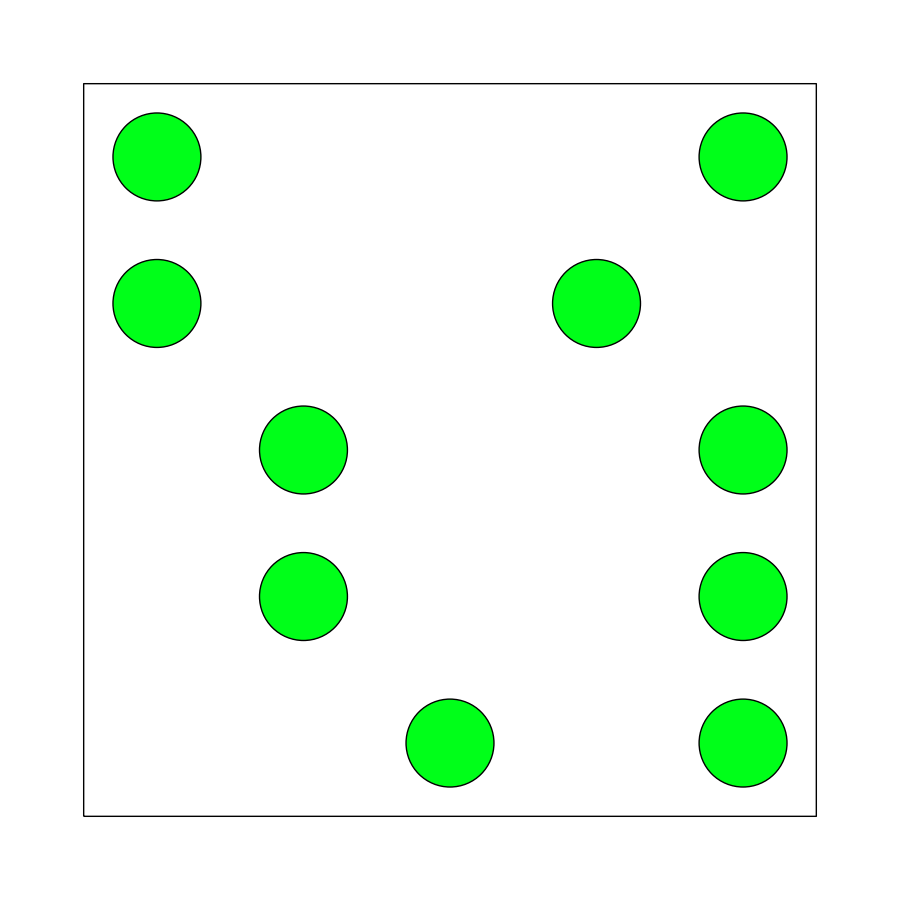

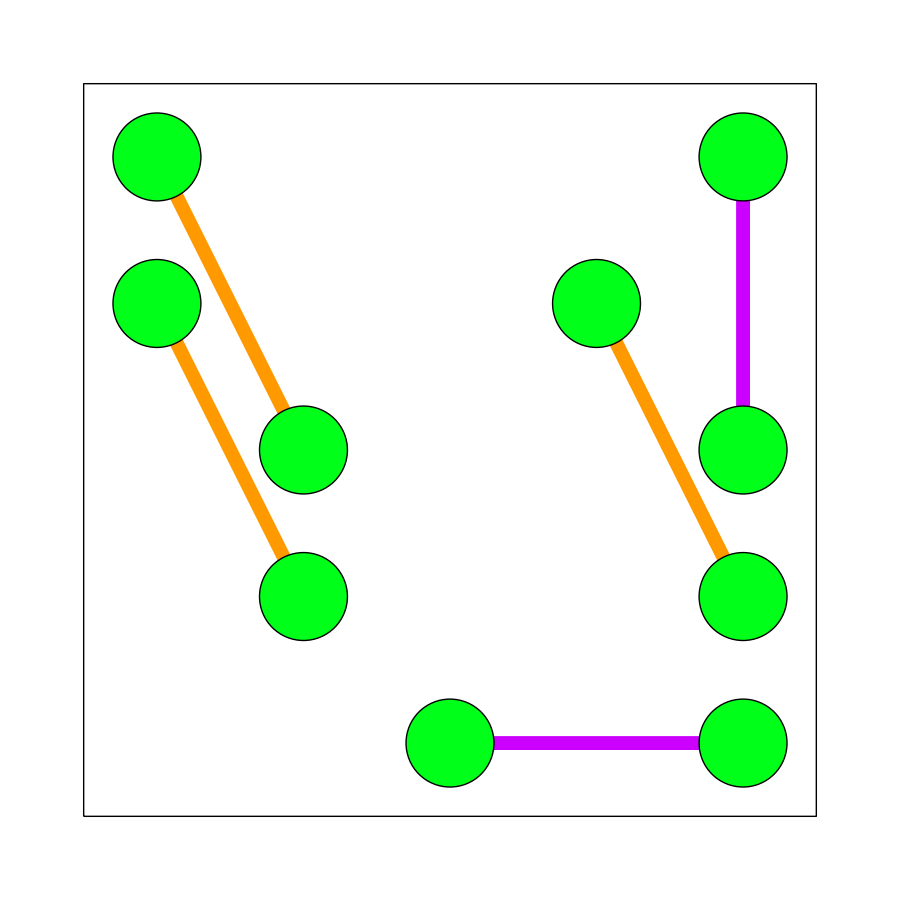

```mathematica
size=5;
num=5;
r:=RandomInteger[{1,size},2];
dists=Drop[Rest[Flatten[Table[x^2+y^2,{x,0,size-1},{y,0,x}]]],-8];
len=Length[dists];
pts={};
dis1=dists⟦RandomInteger[{1,len}]⟧;
dis2=dists⟦RandomInteger[{1,len}]⟧;
While[dis2==dis1||dis1+dis2>2 (size-1)^2,
dis2=dists⟦RandomInteger[{1,len}]⟧];
{dis1,dis2}=Sort[{dis1,dis2}];k=RandomInteger[{1,num-1}];
For[i=1,i≤k,i++,p1=r;p2=r;
While[MemberQ[pts,p1]||MemberQ[pts,p2]||d[{p1,p2}]=!=dis2,p1=r;p2=r];
AppendTo[pts,p1];AppendTo[pts,p2]];
For[i=1,i≤num-k,i++,p1=r;p2=r;While[MemberQ[pts,p1]||MemberQ[pts,p2]||d[{p1,p2}]=!=dis1,p1=r;p2=r];AppendTo[pts,p1];AppendTo[pts,p2]];
pts={{1,4},{1,5},{2,2},{2,3},{3,1},{4,4},{5,1},{5,2},{5,3},{5,5}};dis1=4;dis2=5;
L=Partition[Range[2 num],2];ct=0;While[L=!=0&&ct<2,If[diffdist[L]==2,ct++;answer=L];L=nex[L]];If[ct==1,ans1=Select[answer,d[{pts⟦#1⟦1⟧⟧,pts⟦#1⟦2⟧⟧}]==dis1&];ans2=Select[answer,d[{pts⟦#1⟦1⟧⟧,pts⟦#1⟦2⟧⟧}]==dis2&];pic]
```

```mathematica
size=5;
num=5;
r:=RandomInteger[{1,size},2];
dists=Drop[Rest[Flatten[Table[x^2+y^2,{x,0,size-1},{y,0,x}]]],-8];
len=Length[dists];
While[0==0,
pts={};
dis1=dists⟦RandomInteger[{1,len}]⟧;
dis2=dists⟦RandomInteger[{1,len}]⟧;
While[dis2==dis1||dis1+dis2>2 (size-1)^2,dis2=dists⟦RandomInteger[{1,len}]⟧];{dis1,dis2}=Sort[{dis1,dis2}];k=RandomInteger[{1,num-1}];For[i=1,i≤k,i++,p1=r;p2=r;While[MemberQ[pts,p1]||MemberQ[pts,p2]||d[{p1,p2}]=!=dis2,p1=r;p2=r];AppendTo[pts,p1];AppendTo[pts,p2]];For[i=1,i≤num-k,i++,p1=r;p2=r;While[MemberQ[pts,p1]||MemberQ[pts,p2]||d[{p1,p2}]=!=dis1,p1=r;p2=r];AppendTo[pts,p1];AppendTo[pts,p2]];L=Partition[Range[2 num],2];ct=0;While[L=!=0&&ct<2,If[diffdist[L]==2,ct++;answer=L];L=nex[L]];If[ct==1,ans1=Select[answer,d[{pts⟦#1⟦1⟧⟧,pts⟦#1⟦2⟧⟧}]==dis1&];ans2=Select[answer,d[{pts⟦#1⟦1⟧⟧,pts⟦#1⟦2⟧⟧}]==dis2&];pic]]
```

## 5x5 - 5 pairs

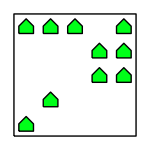

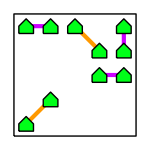

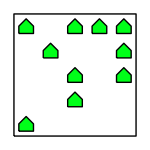

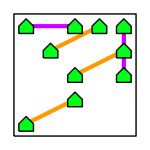

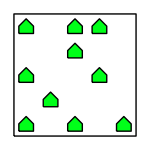

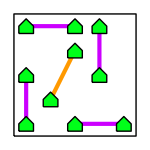

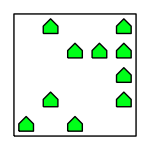

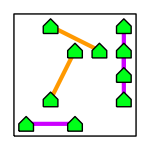

## 5x5 - 6 pairs

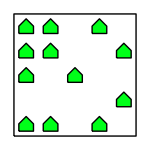

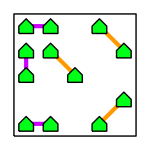

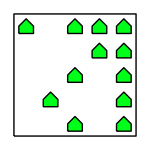

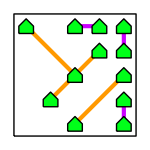

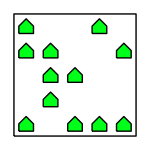

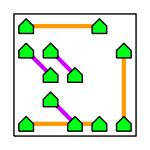

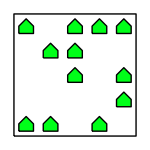

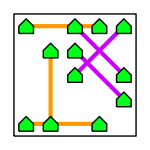

## 6x6 - 6 pairs

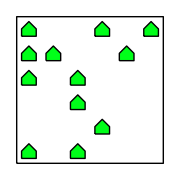

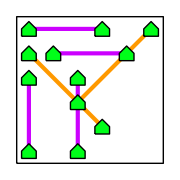

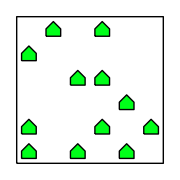

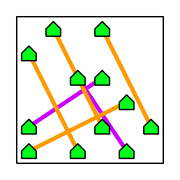

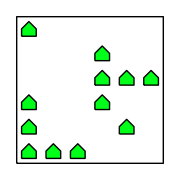

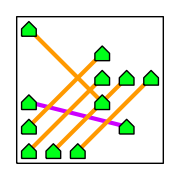

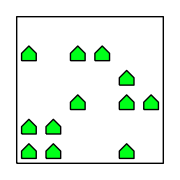

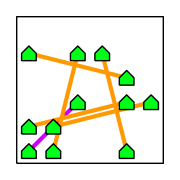

-Graphics-

-Graphics-

-Graphics-

«69 more identical outputs»

## 6x6 - 7 pairs

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## 7x7 - 7 pairs

## 7x7 - 9 pairs

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»